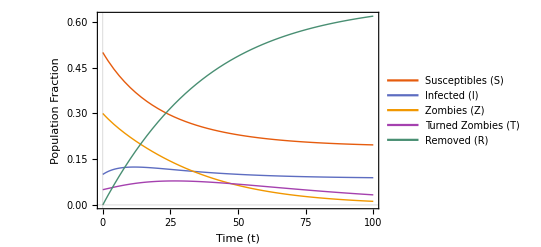

```mathematica
(* Parameters *)
params = {
   beta -> 0.1,    (* Infection rate from Susceptibles to Infected *)
   alphaZ -> 0.2,  (* Rate of Infected turning into Zombies *)
   alphaT -> 0.1,  (* Rate of Infected turning into Turned Zombies *)
   gammaS -> 0.05, (* Rate of Zombies killed by humans *)
   gammaT -> 0.05, (* Rate of Zombies killed by Turned Zombies *)
   deltaS -> 0.02  (* Natural death rate of Turned Zombies *)
};

(* Differential Equations *)
equations = {
   S'[t] == -beta S[t] Z[t],
   Infected'[t] == beta S[t] Z[t] - (alphaZ + alphaT) Infected[t] Z[t],
   Z'[t] == alphaZ Infected[t] Z[t] - gammaS Z[t] - gammaT T[t] Z[t],
   T'[t] == alphaT Infected[t] Z[t] - deltaS T[t],
   R'[t] == gammaS Z[t] + deltaS T[t] + gammaT T[t] Z[t]
};

(* Initial Conditions *)
initialConditions = {
   S[0] == 0.5,  (* Initial fraction of Susceptibles *)
   Infected[0] == 0.1,  (* Initial fraction of Infected *)
   Z[0] == 0.3,  (* Initial fraction of Zombies *)
   T[0] == 0.05, (* Initial fraction of Turned Zombies *)
   R[0] == 0     (* Initially Removed *)
};

(* Solve the System *)
solution = NDSolve[
   Join[equations /. params, initialConditions],
   {S, Infected, Z, T, R},
   {t, 0, 100}
];

(* Plot the Results *)
Plot[
   Evaluate[{S[t], Infected[t], Z[t], T[t], R[t]} /. solution],
   {t, 0, 100},
   PlotLegends -> {"Susceptibles (S)", "Infected (I)", "Zombies (Z)", 
     "Turned Zombies (T)", "Removed (R)"},
   PlotRange -> All,
   PlotStyle -> Thick,
   AxesLabel -> {"Time (t)", "Population Fraction"},
   PlotTheme -> "Scientific"
]
```